```mathematica
nMatrix= Import[NotebookDirectory[]<>"../saved_outputs/cube_3_long.mat"]⟦1⟧;
Dimensions@nMatrix;
nMatrix=Transpose[nMatrix,{1,5,4,2,3}];
{frames,X,Y,Z}=Dimensions[nMatrix]⟦;;-2⟧
θMatrix=ArcTan[nMatrix⟦;;,;;,;;,;;,1⟧,nMatrix⟦;;,;;,;;,;;,2⟧];
```

{20,3,3,8}

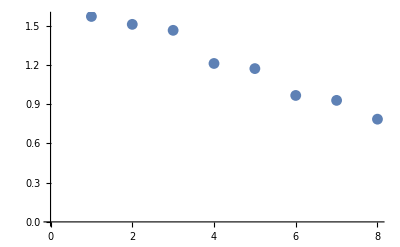

```mathematica
ArcTan@@#&/@nMatrix⟦-1,2,2,;;,{1,2}⟧//ListPlot
```

```mathematica
Dimensions@nMatrix
```

{20,3,3,8,3}

```mathematica
Manipulate[ListVectorPlot[nMatrix⟦frame,;;,;;,zz,;;2⟧,VectorStyle->Arrowheads[0],VectorPoints->All, VectorScale->{.1}],{frame,1,frames,1},{zz,1,Z,1}]
```

```mathematica
nMatrix
```

{{1},{1},16,{{{{0.,1.,0.},{-0.482136,-0.865923,0.133126},{-0.597069,-0.780486,-0.185337},{0.695552,0.707636,-0.124335},{1},{0.68048,0.685037,0.260136},{0.781768,0.602569,0.160464},{0.707107,0.707107,0.}},{1},{1}},{1},{1}},{1}}
 |  |  |  |

```mathematica
SingleBrfMatrix[θ_,Δϕ_]:={{Cos[θ]^2+ⅇ^(-ⅈ Δϕ) Sin[θ]^2,(1-ⅇ^(-ⅈ Δϕ)) Cos[θ] Sin[θ]},{(1-ⅇ^(-ⅈ Δϕ)) Cos[θ] Sin[θ],ⅇ^(-ⅈ Δϕ) Cos[θ]^2+Sin[θ]^2}}
JonesMatrices=Table[Map[Apply[Dot,Reverse[#]]&,Map[SingleBrfMatrix[#,0.6]&,θMatrix⟦frame⟧,{3}],{2}],{frame,Length@θMatrix}];
```

```mathematica
Manipulate[ArrayPlot[Abs@Map[Flatten[#.{{Cos[γ]},{Sin[γ]}}]⟦1⟧&,JonesMatrices⟦frame⟧,{2}],ColorFunction->GrayLevel,ColorFunctionScaling->False],{frame,1,frames,1},{γ,0,π/2}]
```